```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=4;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

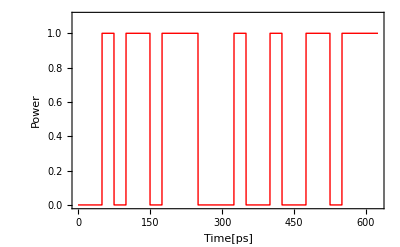

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,1.1}]
```

1/2 (1+Cos[400000000000000 π t])

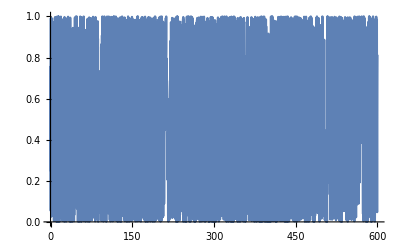

1/2 (1+Cos[400000000000000 π t]) (If[1/40000000000<t<1/20000000000,0,0]+If[1/20000000000<t<3/40000000000,1,0]+If[3/40000000000<t<1/10000000000,0,0]+If[1/10000000000<t<1/8000000000,1,0]+If[1/8000000000<t<3/20000000000,1,0]+If[3/20000000000<t<7/40000000000,0,0]+If[7/40000000000<t<1/5000000000,1,0]+If[1/5000000000<t<9/40000000000,1,0]+If[9/40000000000<t<1/4000000000,1,0]+If[1/4000000000<t<11/40000000000,0,0]+If[11/40000000000<t<3/10000000000,0,0]+If[3/10000000000<t<13/40000000000,0,0]+If[13/40000000000<t<7/20000000000,1,0]+If[7/20000000000<t<3/8000000000,0,0]+If[3/8000000000<t<1/2500000000,0,0]+If[1/2500000000<t<17/40000000000,1,0]+If[17/40000000000<t<9/20000000000,0,0]+If[9/20000000000<t<19/40000000000,0,0]+If[19/40000000000<t<1/2000000000,1,0]+If[1/2000000000<t<21/40000000000,1,0]+If[21/40000000000<t<11/20000000000,0,0]+If[11/20000000000<t<23/40000000000,1,0]+If[23/40000000000<t<3/5000000000,1,0]+If[3/5000000000<t<1/1600000000,1,0]+If[1/1600000000<t<13/20000000000,1,0])

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t_]= (Cos[2*Pi*Fc*t]+1)/2
Plot[carrier[t], {t,0,600}]
cs[t_]=signal[t]*carrier[t]
```

```mathematica
∫_0^(bit*25*10^-12) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))

```mathematica
fc[f_]:=-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))
```

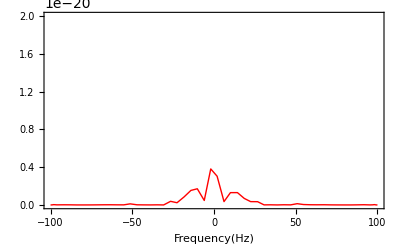

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

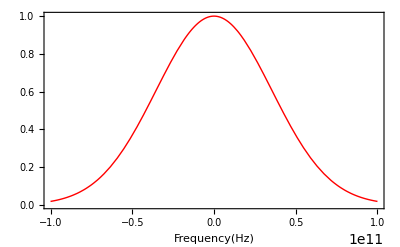

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

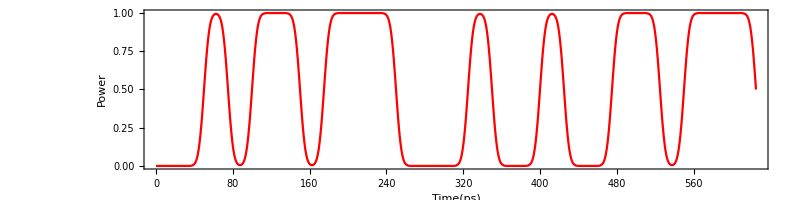

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
(*f[x_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]*)
```

```mathematica
(*max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]*)
```

## Impulse Responce for Fiber Dispersion

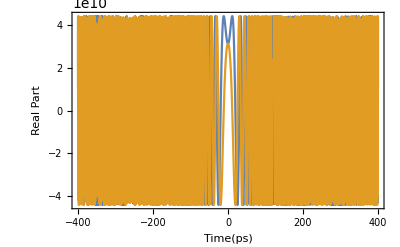

```mathematica
hdis[t_]:=1/(√(2*Pi*β2*L))*Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
(*hcmp[t_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(t^2/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(t^2/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]*)
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
(*For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]*)
```

```mathematica
(*IntegerPart[total*10^12]*)
```

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
(*For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]*)
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

-Graphics-

## Simulation

```mathematica
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*hdis2[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

1.75259×10^7-8.15825×10^6 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,1.93316×10^7},{-99.5,2.22477×10^7},{-99.,2.38483×10^7},{-98.5,2.59776×10^7},{-98.,2.8937×10^7},{-97.5,3.07018×10^7},{-97.,3.01147×10^7},{-96.5,2.85021×10^7},{-96.,2.76418×10^7},{-95.5,2.69046×10^7},{-95.,2.46133×10^7},{-94.5,2.09164×10^7},{-94.,1.7769×10^7},{-93.5,1.69064×10^7},{-93.,1.84761×10^7},{-92.5,2.14585×10^7},{-92.,2.4571×10^7},{-91.5,2.7675×10^7},{-91.,3.18581×10^7},{-90.5,3.69234×10^7},{-90.,4.07681×10^7},{-89.5,4.21804×10^7},{-89.,4.24027×10^7},{-88.5,4.30206×10^7},{-88.,4.31826×10^7},{-87.5,4.10938×10^7},{-87.,3.70251×10^7},{-86.5,3.31282×10^7},{-86.,3.07351×10^7},{-85.5,2.94073×10^7},{-85.,2.88044×10^7},{-84.5,2.94222×10^7},{-84.,3.20755×10^7},{-83.5,3.70385×10^7},{-83.,4.27675×10^7},{-82.5,4.69327×10^7},{-82.,4.90437×10^7},{-81.5,5.06902×10^7},{-81.,5.24551×10^7},{-80.5,5.24876×10^7},{-80.,4.95289×10^7},{-79.5,4.50306×10^7},{-79.,4.10275×10^7},{-78.5,3.72523×10^7},{-78.,3.26134×10^7},{-77.5,2.79879×10^7},{-77.,2.57083×10^7},{-76.5,2.71417×10^7},{-76.,3.12243×10^7},{-75.5,3.5431×10^7},{-75.,3.83916×10^7},{-74.5,4.1174×10^7},{-74.,4.46505×10^7},{-73.5,4.69622×10^7},{-73.,4.64051×10^7},{-72.5,4.43902×10^7},{-72.,4.29574×10^7},{-71.5,4.09589×10^7},{-71.,3.65222×10^7},{-70.5,3.08272×10^7},{-70.,2.62999×10^7},{-69.5,2.28475×10^7},{-69.,1.96451×10^7},{-68.5,1.80585×10^7},{-68.,1.97759×10^7},{-67.5,2.50433×10^7},{-67.,3.21572×10^7},{-66.5,3.82786×10^7},{-66.,4.26693×10^7},{-65.5,4.70985×10^7},{-65.,5.1594×10^7},{-64.5,5.35362×10^7},{-64.,5.22174×10^7},{-63.5,4.98946×10^7},{-63.,4.73324×10^7},{-62.5,4.25089×10^7},{-62.,3.50968×10^7},{-61.5,2.77657×10^7},{-61.,2.26714×10^7},{-60.5,2.03994×10^7},{-60.,2.16×10^7},{-59.5,2.52644×10^7},{-59.,3.06697×10^7},{-58.5,3.75738×10^7},{-58.,4.34498×10^7},{-57.5,4.65914×10^7},{-57.,4.89189×10^7},{-56.5,5.17388×10^7},{-56.,5.2587×10^7},{-55.5,5.03196×10^7},{-55.,4.73911×10^7},{-54.5,4.44999×10^7},{-54.,3.91258×10^7},{-53.5,3.11479×10^7},{-53.,2.3516×10^7},{-52.5,1.8014×10^7},{-52.,1.66099×10^7},{-51.5,2.10091×10^7},{-51.,2.78721×10^7},{-50.5,3.61097×10^7},{-50.,4.49426×10^7},{-49.5,5.12792×10^7},{-49.,5.44699×10^7},{-48.5,5.70823×10^7},{-48.,5.88918×10^7},{-47.5,5.72098×10^7},{-47.,5.30717×10^7},{-46.5,4.91669×10^7},{-46.,4.38693×10^7},{-45.5,3.52468×10^7},{-45.,2.56443×10^7},{-44.5,1.69613×10^7},{-44.,9.81245×10^6},{-43.5,1.36165×10^7},{-43.,2.33819×10^7},{-42.5,3.3763×10^7},{-42.,4.50066×10^7},{-41.5,5.41475×10^7},{-41.,5.94266×10^7},{-40.5,6.33718×10^7},{-40.,6.63939×10^7},{-39.5,6.56032×10^7},{-39.,6.19902×10^7},{-38.5,5.84908×10^7},{-38.,5.30631×10^7},{-37.5,4.38357×10^7},{-37.,3.36301×10^7},{-36.5,2.28429×10^7},{-36.,8.55003×10^6},{-35.5,7.74815×10^6},{-35.,2.26151×10^7},{-34.5,3.71307×10^7},{-34.,5.20813×10^7},{-33.5,6.36318×10^7},{-33.,7.07733×10^7},{-32.5,7.64864×10^7},{-32.,7.98254×10^7},{-31.5,7.87987×10^7},{-31.,7.68051×10^7},{-30.5,7.50664×10^7},{-30.,6.98735×10^7},{-29.5,6.19941×10^7},{-29.,5.32714×10^7},{-28.5,4.04167×10^7},{-28.,2.60146×10^7},{-27.5,2.46108×10^7},{-27.,3.77555×10^7},{-26.5,5.80186×10^7},{-26.,7.85744×10^7},{-25.5,9.37016×10^7},{-25.,1.05109×10^8},{-24.5,1.13805×10^8},{-24.,1.17451×10^8},{-23.5,1.19528×10^8},{-23.,1.2355×10^8},{-22.5,1.25767×10^8},{-22.,1.25722×10^8},{-21.5,1.24485×10^8},{-21.,1.17794×10^8},{-20.5,1.07817×10^8},{-20.,1.03463×10^8},{-19.5,1.08133×10^8},{-19.,1.26027×10^8},{-18.5,1.54899×10^8},{-18.,1.84153×10^8},{-17.5,2.11758×10^8},{-17.,2.37803×10^8},{-16.5,2.59159×10^8},{-16.,2.79749×10^8},{-15.5,3.03547×10^8},{-15.,3.27204×10^8},{-14.5,3.51349×10^8},{-14.,3.76404×10^8},{-13.5,3.97424×10^8},{-13.,4.16792×10^8},{-12.5,4.39617×10^8},{-12.,4.65937×10^8},{-11.5,5.01256×10^8},{-11.,5.49493×10^8},{-10.5,6.065×10^8},{-10.,6.73337×10^8},{-9.5,7.50062×10^8},{-9.,8.31588×10^8},{-8.5,9.19648×10^8},{-8.,1.01496×10^9},{-7.5,1.11356×10^9},{-7.,1.21861×10^9},{-6.5,1.33235×10^9},{-6.,1.45252×10^9},{-5.5,1.58309×10^9},{-5.,1.72533×10^9},{-4.5,1.87518×10^9},{-4.,2.03542×10^9},{-3.5,2.20778×10^9},{-3.,2.39172×10^9},{-2.5,2.59509×10^9},{-2.,2.82303×10^9},{-1.5,3.07534×10^9},{-1.,3.3562×10^9},{-0.5,3.66432×10^9},{0.,3.99485×10^9},{0.5,4.35097×10^9},{1.,4.73387×10^9},{1.5,5.14374×10^9},{2.,5.58777×10^9},{2.5,6.06766×10^9},{3.,6.58181×10^9},{3.5,7.13423×10^9},{4.,7.72395×10^9},{4.5,8.34946×10^9},{5.,9.01632×10^9},{5.5,9.72525×10^9},{6.,1.04766×10^10},{6.5,1.12772×10^10},{7.,1.21285×10^10},{7.5,1.30328×10^10},{8.,1.39984×10^10},{8.5,1.50268×10^10},{9.,1.61189×10^10},{9.5,1.72796×10^10},{10.,1.85066×10^10},{10.5,1.98002×10^10},{11.,2.11671×10^10},{11.5,2.26092×10^10},{12.,2.41314×10^10},{12.5,2.57423×10^10},{13.,2.74426×10^10},{13.5,2.92345×10^10},{14.,3.11239×10^10},{14.5,3.31104×10^10},{15.,3.51988×10^10},{15.5,3.73978×10^10},{16.,3.97104×10^10},{16.5,4.21448×10^10},{17.,4.4712×10^10},{17.5,4.74181×10^10},{18.,5.02759×10^10},{18.5,5.33003×10^10},{19.,5.65008×10^10},{19.5,5.98918×10^10},{20.,6.3488×10^10},{20.5,6.72983×10^10},{21.,7.1339×10^10},{21.5,7.56277×10^10},{22.,8.01783×10^10},{22.5,8.50113×10^10},{23.,9.01454×10^10},{23.5,9.55926×10^10},{24.,1.01369×10^11},{24.5,1.07489×10^11},{25.,1.13957×10^11},{25.5,1.20786×10^11},{26.,1.27981×10^11},{26.5,1.35539×10^11},{27.,1.43462×10^11},{27.5,1.51743×10^11},{28.,1.60372×10^11},{28.5,1.6934×10^11},{29.,1.78636×10^11},{29.5,1.88239×10^11},{30.,1.98131×10^11},{30.5,2.08288×10^11},{31.,2.1868×10^11},{31.5,2.29282×10^11},{32.,2.40065×10^11},{32.5,2.51001×10^11},{33.,2.62068×10^11},{33.5,2.73244×10^11},{34.,2.8451×10^11},{34.5,2.95862×10^11},{35.,3.07296×10^11},{35.5,3.18823×10^11},{36.,3.30469×10^11},{36.5,3.42264×10^11},{37.,3.54255×10^11},{37.5,3.66505×10^11},{38.,3.79086×10^11},{38.5,3.92088×10^11},{39.,4.05619×10^11},{39.5,4.1979×10^11},{40.,4.3473×10^11},{40.5,4.50574×10^11},{41.,4.67455×10^11},{41.5,4.85516×10^11},{42.,5.04895×10^11},{42.5,5.25722×10^11},{43.,5.48122×10^11},{43.5,5.72208×10^11},{44.,5.98075×10^11},{44.5,6.25807×10^11},{45.,6.55472×10^11},{45.5,6.87117×10^11},{46.,7.2078×10^11},{46.5,7.56474×10^11},{47.,7.94194×10^11},{47.5,8.33916×10^11},{48.,8.75593×10^11},{48.5,9.1915×10^11},{49.,9.64493×10^11},{49.5,1.0115×10^12},{50.,1.06×10^12},{50.5,1.10981×10^12},{51.,1.16071×10^12},{51.5,1.21243×10^12},{52.,1.26468×10^12},{52.5,1.31715×10^12},{53.,1.36947×10^12},{53.5,1.4213×10^12},{54.,1.47224×10^12},{54.5,1.5219×10^12},{55.,1.5699×10^12},{55.5,1.61587×10^12},{56.,1.65945×10^12},{56.5,1.70034×10^12},{57.,1.73823×10^12},{57.5,1.77292×10^12},{58.,1.80421×10^12},{58.5,1.83198×10^12},{59.,1.85618×10^12},{59.5,1.8768×10^12},{60.,1.89388×10^12},{60.5,1.90753×10^12},{61.,1.91788×10^12},{61.5,1.92509×10^12},{62.,1.92933×10^12},{62.5,1.93078×10^12},{63.,1.9296×10^12},{63.5,1.92591×10^12},{64.,1.9198×10^12},{64.5,1.9113×10^12},{65.,1.90038×10^12},{65.5,1.88698×10^12},{66.,1.87095×10^12},{66.5,1.85212×10^12},{67.,1.83026×10^12},{67.5,1.80515×10^12},{68.,1.77655×10^12},{68.5,1.74423×10^12},{69.,1.70799×10^12},{69.5,1.66771×10^12},{70.,1.62329×10^12},{70.5,1.57475×10^12},{71.,1.52216×10^12},{71.5,1.46572×10^12},{72.,1.40573×10^12},{72.5,1.34258×10^12},{73.,1.27675×10^12},{73.5,1.20884×10^12},{74.,1.13954×10^12},{74.5,1.06962×10^12},{75.,9.99931×10^11},{75.5,9.31387×10^11},{76.,8.64973×10^11},{76.5,8.01719×10^11},{77.,7.427×10^11},{77.5,6.8901×10^11},{78.,6.41714×10^11},{78.5,6.01794×10^11},{79.,5.70046×10^11},{79.5,5.46959×10^11},{80.,5.32617×10^11},{80.5,5.26645×10^11},{81.,5.28238×10^11},{81.5,5.3629×10^11},{82.,5.49537×10^11},{82.5,5.667×10^11},{83.,5.86582×10^11},{83.5,6.08103×10^11},{84.,6.3031×10^11},{84.5,6.52361×10^11},{85.,6.73502×10^11},{85.5,6.9306×10^11},{86.,7.10424×10^11},{86.5,7.25044×10^11},{87.,7.3644×10^11},{87.5,7.442×10^11},{88.,7.47997×10^11},{88.5,7.47613×10^11},{89.,7.42939×10^11},{89.5,7.34014×10^11},{90.,7.21026×10^11},{90.5,7.04336×10^11},{91.,6.84505×10^11},{91.5,6.62306×10^11},{92.,6.38755×10^11},{92.5,6.15123×10^11},{93.,5.92926×10^11},{93.5,5.73905×10^11},{94.,5.59913×10^11},{94.5,5.52746×10^11},{95.,5.53886×10^11},{95.5,5.64233×10^11},{96.,5.83967×10^11},{96.5,6.12549×10^11},{97.,6.48902×10^11},{97.5,6.91647×10^11},{98.,7.39314×10^11},{98.5,7.90499×10^11},{99.,8.43935×10^11},{99.5,8.98537×10^11},{100.,9.53397×10^11},{100.5,1.00778×10^12},{101.,1.06111×10^12},{101.5,1.11298×10^12},{102.,1.1631×10^12},{102.5,1.21131×10^12},{103.,1.25756×10^12},{103.5,1.30189×10^12},{104.,1.34441×10^12},{104.5,1.3853×10^12},{105.,1.42476×10^12},{105.5,1.46301×10^12},{106.,1.50029×10^12},{106.5,1.5368×10^12},{107.,1.57275×10^12},{107.5,1.60828×10^12},{108.,1.64351×10^12},{108.5,1.67849×10^12},{109.,1.71324×10^12},{109.5,1.74772×10^12},{110.,1.78186×10^12},{110.5,1.81551×10^12},{111.,1.84851×10^12},{111.5,1.88065×10^12},{112.,1.9117×10^12},{112.5,1.9414×10^12},{113.,1.9695×10^12},{113.5,1.99574×10^12},{114.,2.01991×10^12},{114.5,2.04181×10^12},{115.,2.06129×10^12},{115.5,2.07828×10^12},{116.,2.09274×10^12},{116.5,2.10471×10^12},{117.,2.1143×10^12},{117.5,2.12167×10^12},{118.,2.12701×10^12},{118.5,2.13057×10^12},{119.,2.13259×10^12},{119.5,2.13334×10^12},{120.,2.13309×10^12},{120.5,2.13209×10^12},{121.,2.13058×10^12},{121.5,2.12877×10^12},{122.,2.12684×10^12},{122.5,2.12496×10^12},{123.,2.12325×10^12},{123.5,2.12183×10^12},{124.,2.12077×10^12},{124.5,2.12012×10^12},{125.,2.11992×10^12},{125.5,2.12017×10^12},{126.,2.12086×10^12},{126.5,2.12195×10^12},{127.,2.12338×10^12},{127.5,2.12507×10^12},{128.,2.12692×10^12},{128.5,2.12879×10^12},{129.,2.13055×10^12},{129.5,2.132×10^12},{130.,2.13294×10^12},{130.5,2.13316×10^12},{131.,2.1324×10^12},{131.5,2.1304×10^12},{132.,2.12689×10^12},{132.5,2.12162×10^12},{133.,2.11435×10^12},{133.5,2.10485×10^12},{134.,2.09296×10^12},{134.5,2.07857×10^12},{135.,2.06163×10^12},{135.5,2.04214×10^12},{136.,2.02018×10^12},{136.5,1.99591×10^12},{137.,1.96953×10^12},{137.5,1.94126×10^12},{138.,1.91138×10^12},{138.5,1.88017×10^12},{139.,1.8479×10^12},{139.5,1.81484×10^12},{140.,1.7812×10^12},{140.5,1.74716×10^12},{141.,1.71287×10^12},{141.5,1.67839×10^12},{142.,1.64374×10^12},{142.5,1.60888×10^12},{143.,1.5737×10^12},{143.5,1.53805×10^12},{144.,1.50174×10^12},{144.5,1.46454×10^12},{145.,1.4262×10^12},{145.5,1.38648×10^12},{146.,1.34516×10^12},{146.5,1.30203×10^12},{147.,1.25697×10^12},{147.5,1.20992×10^12},{148.,1.16092×10^12},{148.5,1.1101×10^12},{149.,1.05773×10^12},{149.5,1.00417×10^12},{150.,9.49934×10^11},{150.5,8.9565×10^11},{151.,8.42071×10^11},{151.5,7.90085×10^11},{152.,7.40694×10^11},{152.5,6.94996×10^11},{153.,6.54156×10^11},{153.5,6.19327×10^11},{154.,5.91558×10^11},{154.5,5.71632×10^11},{155.,5.59932×10^11},{155.5,5.56327×10^11},{156.,5.6017×10^11},{156.5,5.70385×10^11},{157.,5.85625×10^11},{157.5,6.04457×10^11},{158.,6.25481×10^11},{158.5,6.47423×10^11},{159.,6.69165×10^11},{159.5,6.89757×10^11},{160.,7.08414×10^11},{160.5,7.24495×10^11},{161.,7.375×10^11},{161.5,7.47047×10^11},{162.,7.52877×10^11},{162.5,7.54838×10^11},{163.,7.52885×10^11},{163.5,7.47072×10^11},{164.,7.37563×10^11},{164.5,7.24627×10^11},{165.,7.0864×10^11},{165.5,6.90104×10^11},{166.,6.69647×10^11},{166.5,6.4805×10^11},{167.,6.2624×10^11},{167.5,6.05323×10^11},{168.,5.86558×10^11},{168.5,5.7133×10^11},{169.,5.61059×10^11},{169.5,5.57077×10^11},{170.,5.60451×10^11},{170.5,5.71825×10^11},{171.,5.91326×10^11},{171.5,6.18587×10^11},{172.,6.52841×10^11},{172.5,6.93074×10^11},{173.,7.38177×10^11},{173.5,7.87043×10^11},{174.,8.38636×10^11},{174.5,8.92017×10^11},{175.,9.46371×10^11},{175.5,1.00099×10^12},{176.,1.05527×10^12},{176.5,1.1087×10^12},{177.,1.1609×10^12},{177.5,1.21153×10^12},{178.,1.26036×10^12},{178.5,1.30721×10^12},{179.,1.35199×10^12},{179.5,1.39468×10^12},{180.,1.4353×10^12},{180.5,1.47395×10^12},{181.,1.51076×10^12},{181.5,1.54593×10^12},{182.,1.57965×10^12},{182.5,1.61219×10^12},{183.,1.6438×10^12},{183.5,1.67473×10^12},{184.,1.70523×10^12},{184.5,1.73553×10^12},{185.,1.76581×10^12},{185.5,1.79618×10^12},{186.,1.82673×10^12},{186.5,1.85745×10^12},{187.,1.88827×10^12},{187.5,1.91905×10^12},{188.,1.94959×10^12},{188.5,1.97962×10^12},{189.,2.00884×10^12},{189.5,2.0369×10^12},{190.,2.06346×10^12},{190.5,2.08817×10^12},{191.,2.11071×10^12},{191.5,2.13076×10^12},{192.,2.1481×10^12},{192.5,2.16251×10^12},{193.,2.17387×10^12},{193.5,2.18211×10^12},{194.,2.18721×10^12},{194.5,2.18922×10^12},{195.,2.18825×10^12},{195.5,2.18443×10^12},{196.,2.17794×10^12},{196.5,2.16901×10^12},{197.,2.15787×10^12},{197.5,2.14478×10^12},{198.,2.13004×10^12},{198.5,2.11393×10^12},{199.,2.0968×10^12},{199.5,2.07896×10^12},{200.,2.06076×10^12},{200.5,2.04257×10^12},{201.,2.02475×10^12},{201.5,2.00766×10^12},{202.,1.99166×10^12},{202.5,1.97709×10^12},{203.,1.96429×10^12},{203.5,1.95352×10^12},{204.,1.94504×10^12},{204.5,1.93902×10^12},{205.,1.93559×10^12},{205.5,1.93479×10^12},{206.,1.93656×10^12},{206.5,1.94078×10^12},{207.,1.94721×10^12},{207.5,1.95555×10^12},{208.,1.9654×10^12},{208.5,1.97629×10^12},{209.,1.98771×10^12},{209.5,1.99912×10^12},{210.,2.00997×10^12},{210.5,2.01975×10^12},{211.,2.02795×10^12},{211.5,2.03418×10^12},{212.,2.03812×10^12},{212.5,2.03956×10^12},{213.,2.03842×10^12},{213.5,2.03476×10^12},{214.,2.02872×10^12},{214.5,2.02061×10^12},{215.,2.01082×10^12},{215.5,1.99982×10^12},{216.,1.98815×10^12},{216.5,1.97638×10^12},{217.,1.96508×10^12},{217.5,1.95483×10^12},{218.,1.94611×10^12},{218.5,1.93939×10^12},{219.,1.93502×10^12},{219.5,1.93326×10^12},{220.,1.93426×10^12},{220.5,1.93808×10^12},{221.,1.94466×10^12},{221.5,1.95384×10^12},{222.,1.96538×10^12},{222.5,1.97897×10^12},{223.,1.99424×10^12},{223.5,2.01079×10^12},{224.,2.02819×10^12},{224.5,2.04604×10^12},{225.,2.06393×10^12},{225.5,2.08147×10^12},{226.,2.09832×10^12},{226.5,2.11418×10^12},{227.,2.12878×10^12},{227.5,2.1419×10^12},{228.,2.15336×10^12},{228.5,2.16298×10^12},{229.,2.17063×10^12},{229.5,2.17619×10^12},{230.,2.17956×10^12},{230.5,2.18063×10^12},{231.,2.17933×10^12},{231.5,2.17559×10^12},{232.,2.16934×10^12},{232.5,2.16055×10^12},{233.,2.14921×10^12},{233.5,2.13531×10^12},{234.,2.1189×10^12},{234.5,2.10003×10^12},{235.,2.07879×10^12},{235.5,2.05529×10^12},{236.,2.02966×10^12},{236.5,2.00206×10^12},{237.,1.97263×10^12},{237.5,1.94154×10^12},{238.,1.90896×10^12},{238.5,1.87505×10^12},{239.,1.83997×10^12},{239.5,1.80386×10^12},{240.,1.76687×10^12},{240.5,1.72912×10^12},{241.,1.69073×10^12},{241.5,1.65183×10^12},{242.,1.61251×10^12},{242.5,1.57287×10^12},{243.,1.53302×10^12},{243.5,1.49305×10^12},{244.,1.45304×10^12},{244.5,1.41311×10^12},{245.,1.37333×10^12},{245.5,1.33379×10^12},{246.,1.29458×10^12},{246.5,1.25576×10^12},{247.,1.21742×10^12},{247.5,1.1796×10^12},{248.,1.14236×10^12},{248.5,1.10575×10^12},{249.,1.0698×10^12},{249.5,1.03453×10^12},{250.,9.99972×10^11},{250.5,9.66128×10^11},{251.,9.33014×10^11},{251.5,9.00631×10^11},{252.,8.6899×10^11},{252.5,8.38097×10^11},{253.,8.07959×10^11},{253.5,7.78587×10^11},{254.,7.49992×10^11},{254.5,7.22182×10^11},{255.,6.95166×10^11},{255.5,6.68948×10^11},{256.,6.43523×10^11},{256.5,6.18885×10^11},{257.,5.95015×10^11},{257.5,5.71891×10^11},{258.,5.49484×10^11},{258.5,5.27766×10^11},{259.,5.06703×10^11},{259.5,4.86279×10^11},{260.,4.66472×10^11},{260.5,4.47278×10^11},{261.,4.28699×10^11},{261.5,4.10748×10^11},{262.,3.93436×10^11},{262.5,3.76779×10^11},{263.,3.60781×10^11},{263.5,3.45431×10^11},{264.,3.30708×10^11},{264.5,3.16562×10^11},{265.,3.02937×10^11},{265.5,2.89763×10^11},{266.,2.76973×10^11},{266.5,2.64507×10^11},{267.,2.52339×10^11},{267.5,2.40463×10^11},{268.,2.28918×10^11},{268.5,2.17772×10^11},{269.,2.07114×10^11},{269.5,1.97044×10^11},{270.,1.8764×10^11},{270.5,1.78941×10^11},{271.,1.7092×10^11},{271.5,1.63487×10^11},{272.,1.56477×10^11},{272.5,1.4969×10^11},{273.,1.42911×10^11},{273.5,1.35954×10^11},{274.,1.28702×10^11},{274.5,1.2114×10^11},{275.,1.13365×10^11},{275.5,1.05607×10^11},{276.,9.82018×10^10},{276.5,9.15491×10^10},{277.,8.60384×10^10},{277.5,8.19185×10^10},{278.,7.91972×10^10},{278.5,7.75871×10^10},{279.,7.6569×10^10},{279.5,7.55072×10^10},{280.,7.38088×10^10},{280.5,7.09923×10^10},{281.,6.67585×10^10},{281.5,6.10032×10^10},{282.,5.383×10^10},{282.5,4.5582×10^10},{283.,3.69268×10^10},{283.5,2.90893×10^10},{284.,2.42098×10^10},{284.5,2.45147×10^10},{285.,2.93203×10^10},{285.5,3.58976×10^10},{286.,4.22495×10^10},{286.5,4.73006×10^10},{287.,5.04628×10^10},{287.5,5.14481×10^10},{288.,5.01703×10^10},{288.5,4.67485×10^10},{289.,4.15123×10^10},{289.5,3.50684×10^10},{290.,2.85288×10^10},{290.5,2.38964×10^10},{291.,2.38115×10^10},{291.5,2.87289×10^10},{292.,3.63962×10^10},{292.5,4.4777×10^10},{293.,5.27259×10^10},{293.5,5.96308×10^10},{294.,6.51841×10^10},{294.5,6.92976×10^10},{295.,7.20818×10^10},{295.5,7.38231×10^10},{296.,7.49747×10^10},{296.5,7.6108×10^10},{297.,7.78284×10^10},{297.5,8.06557×10^10},{298.,8.48951×10^10},{298.5,9.05778×10^10},{299.,9.74933×10^10},{299.5,1.05288×10^11},{300.,1.13574×10^11},{300.5,1.22012×10^11},{301.,1.30356×10^11},{301.5,1.38477×10^11},{302.,1.46365×10^11},{302.5,1.541×10^11},{303.,1.61847×10^11},{303.5,1.69794×10^11},{304.,1.7813×10^11},{304.5,1.87002×10^11},{305.,1.96481×10^11},{305.5,2.06574×10^11},{306.,2.17203×10^11},{306.5,2.28252×10^11},{307.,2.39581×10^11},{307.5,2.51046×10^11},{308.,2.62541×10^11},{308.5,2.73986×10^11},{309.,2.85354×10^11},{309.5,2.96658×10^11},{310.,3.07936×10^11},{310.5,3.19261×10^11},{311.,3.30701×10^11},{311.5,3.42336×10^11},{312.,3.54238×10^11},{312.5,3.66466×10^11},{313.,3.79087×10^11},{313.5,3.92157×10^11},{314.,4.05749×10^11},{314.5,4.19946×10^11},{315.,4.34848×10^11},{315.5,4.5058×10^11},{316.,4.6728×10^11},{316.5,4.85107×10^11},{317.,5.04225×10^11},{317.5,5.24804×10^11},{318.,5.47006×10^11},{318.5,5.70981×10^11},{319.,5.96858×10^11},{319.5,6.24742×10^11},{320.,6.54707×10^11},{320.5,6.86795×10^11},{321.,7.21018×10^11},{321.5,7.57352×10^11},{322.,7.95745×10^11},{322.5,8.36117×10^11},{323.,8.78356×10^11},{323.5,9.22337×10^11},{324.,9.67902×10^11},{324.5,1.01488×10^12},{325.,1.06309×10^12},{325.5,1.11231×10^12},{326.,1.16233×10^12},{326.5,1.21292×10^12},{327.,1.26381×10^12},{327.5,1.31477×10^12},{328.,1.36551×10^12},{328.5,1.41577×10^12},{329.,1.46528×10^12},{329.5,1.51376×10^12},{330.,1.56094×10^12},{330.5,1.60655×10^12},{331.,1.65034×10^12},{331.5,1.69205×10^12},{332.,1.73144×10^12},{332.5,1.76828×10^12},{333.,1.80234×10^12},{333.5,1.83342×10^12},{334.,1.86132×10^12},{334.5,1.88587×10^12},{335.,1.90689×10^12},{335.5,1.92426×10^12},{336.,1.93785×10^12},{336.5,1.94758×10^12},{337.,1.95338×10^12},{337.5,1.95521×10^12},{338.,1.95309×10^12},{338.5,1.94704×10^12},{339.,1.93712×10^12},{339.5,1.9234×10^12},{340.,1.90601×10^12},{340.5,1.88507×10^12},{341.,1.86072×10^12},{341.5,1.83311×10^12},{342.,1.80239×10^12},{342.5,1.76873×10^12},{343.,1.7323×10^12},{343.5,1.69327×10^12},{344.,1.65181×10^12},{344.5,1.60814×10^12},{345.,1.56245×10^12},{345.5,1.51499×10^12},{346.,1.46603×10^12},{346.5,1.41586×10^12},{347.,1.3648×10^12},{347.5,1.31321×10^12},{348.,1.26145×10^12},{348.5,1.2099×10^12},{349.,1.15891×10^12},{349.5,1.10883×10^12},{350.,1.05996×10^12},{350.5,1.01254×10^12},{351.,9.66755×10^11},{351.5,9.22732×10^11},{352.,8.80515×10^11},{352.5,8.40093×10^11},{353.,8.01404×10^11},{353.5,7.64352×10^11},{354.,7.28829×10^11},{354.5,6.9472×10^11},{355.,6.61938×10^11},{355.5,6.30424×10^11},{356.,6.00161×10^11},{356.5,5.71195×10^11},{357.,5.43616×10^11},{357.5,5.17581×10^11},{358.,4.93296×10^11},{358.5,4.70999×10^11},{359.,4.50943×10^11},{359.5,4.33354×10^11},{360.,4.18382×10^11},{360.5,4.06056×10^11},{361.,3.96239×10^11},{361.5,3.88595×10^11},{362.,3.82612×10^11},{362.5,3.77612×10^11},{363.,3.72833×10^11},{363.5,3.67481×10^11},{364.,3.60798×10^11},{364.5,3.52129×10^11},{365.,3.4096×10^11},{365.5,3.26952×10^11},{366.,3.09967×10^11},{366.5,2.90088×10^11},{367.,2.67622×10^11},{367.5,2.43147×10^11},{368.,2.17534×10^11},{368.5,1.92031×10^11},{369.,1.68376×10^11},{369.5,1.48862×10^11},{370.,1.36144×10^11},{370.5,1.32266×10^11},{371.,1.37284×10^11},{371.5,1.49042×10^11},{372.,1.64497×10^11},{372.5,1.80975×10^11},{373.,1.96503×10^11},{373.5,2.09728×10^11},{374.,2.19742×10^11},{374.5,2.25967×10^11},{375.,2.28075×10^11},{375.5,2.25964×10^11},{376.,2.1974×10^11},{376.5,2.09722×10^11},{377.,1.96497×10^11},{377.5,1.80968×10^11},{378.,1.64491×10^11},{378.5,1.49037×10^11},{379.,1.37287×10^11},{379.5,1.32273×10^11},{380.,1.36157×10^11},{380.5,1.48881×10^11},{381.,1.68395×10^11},{381.5,1.9205×10^11},{382.,2.17551×10^11},{382.5,2.43161×10^11},{383.,2.67631×10^11},{383.5,2.90091×10^11},{384.,3.09969×10^11},{384.5,3.26946×10^11},{385.,3.40952×10^11},{385.5,3.52118×10^11},{386.,3.60785×10^11},{386.5,3.67465×10^11},{387.,3.7282×10^11},{387.5,3.77597×10^11},{388.,3.82597×10^11},{388.5,3.88585×10^11},{389.,3.96231×10^11},{389.5,4.06052×10^11},{390.,4.18384×10^11},{390.5,4.33361×10^11},{391.,4.50958×10^11},{391.5,4.7102×10^11},{392.,4.93323×10^11},{392.5,5.17609×10^11},{393.,5.43643×10^11},{393.5,5.71216×10^11},{394.,6.00175×10^11},{394.5,6.30424×10^11},{395.,6.61927×10^11},{395.5,6.94695×10^11},{396.,7.28792×10^11},{396.5,7.6431×10^11},{397.,8.01358×10^11},{397.5,8.4005×10^11},{398.,8.80484×10^11},{398.5,9.22716×10^11},{399.,9.66758×10^11},{399.5,1.01256×10^12},{400.,1.06×10^12},{400.5,1.10889×10^12},{401.,1.15899×10^12},{401.5,1.20998×10^12},{402.,1.26152×10^12},{402.5,1.31326×10^12},{403.,1.36483×10^12},{403.5,1.41585×10^12},{404.,1.46598×10^12},{404.5,1.51491×10^12},{405.,1.56233×10^12},{405.5,1.608×10^12},{406.,1.65167×10^12},{406.5,1.69314×10^12},{407.,1.73221×10^12},{407.5,1.76869×10^12},{408.,1.80242×10^12},{408.5,1.83321×10^12},{409.,1.8609×10^12},{409.5,1.88531×10^12},{410.,1.90629×10^12},{410.5,1.92369×10^12},{411.,1.93738×10^12},{411.5,1.94723×10^12},{412.,1.95317×10^12},{412.5,1.95516×10^12},{413.,1.95315×10^12},{413.5,1.94719×10^12},{414.,1.93733×10^12},{414.5,1.92364×10^12},{415.,1.90624×10^12},{415.5,1.88527×10^12},{416.,1.86087×10^12},{416.5,1.83321×10^12},{417.,1.80244×10^12},{417.5,1.76873×10^12},{418.,1.73226×10^12},{418.5,1.6932×10^12},{419.,1.65173×10^12},{419.5,1.60804×10^12},{420.,1.56235×10^12},{420.5,1.51491×10^12},{421.,1.46596×10^12},{421.5,1.4158×10^12},{422.,1.36476×10^12},{422.5,1.3132×10^12},{423.,1.26146×10^12},{423.5,1.20993×10^12},{424.,1.15897×10^12},{424.5,1.10891×10^12},{425.,1.06004×10^12},{425.5,1.01263×10^12},{426.,9.66842×10^11},{426.5,9.22798×10^11},{427.,8.80551×10^11},{427.5,8.4009×10^11},{428.,8.01357×10^11},{428.5,7.64263×10^11},{429.,7.28707×10^11},{429.5,6.9458×10^11},{430.,6.61798×10^11},{430.5,6.30306×10^11},{431.,6.00091×10^11},{431.5,5.71186×10^11},{432.,5.43683×10^11},{432.5,5.17724×10^11},{433.,4.935×10^11},{433.5,4.71237×10^11},{434.,4.5118×10^11},{434.5,4.33541×10^11},{435.,4.18475×10^11},{435.5,4.0602×10^11},{436.,3.96059×10^11},{436.5,3.88282×10^11},{437.,3.82205×10^11},{437.5,3.77179×10^11},{438.,3.72455×10^11},{438.5,3.67235×10^11},{439.,3.60759×10^11},{439.5,3.52338×10^11},{440.,3.41424×10^11},{440.5,3.27632×10^11},{441.,3.10787×10^11},{441.5,2.9092×10^11},{442.,2.68316×10^11},{442.5,2.43537×10^11},{443.,2.17468×10^11},{443.5,1.91407×10^11},{444.,1.67201×10^11},{444.5,1.4734×10^11},{445.,1.3471×10^11},{445.5,1.3149×10^11},{446.,1.37559×10^11},{446.5,1.50385×10^11},{447.,1.66658×10^11},{447.5,1.83577×10^11},{448.,1.9915×10^11},{448.5,2.12038×10^11},{449.,2.21385×10^11},{449.5,2.26678×10^11},{450.,2.27671×10^11},{450.5,2.24349×10^11},{451.,2.16908×10^11},{451.5,2.05755×10^11},{452.,1.91524×10^11},{452.5,1.75154×10^11},{453.,1.57986×10^11},{453.5,1.41934×10^11},{454.,1.29596×10^11},{454.5,1.23953×10^11},{455.,1.27163×10^11},{455.5,1.3917×10^11},{456.,1.5794×10^11},{456.5,1.80891×10^11},{457.,2.05853×10^11},{457.5,2.31229×10^11},{458.,2.55891×10^11},{458.5,2.79057×10^11},{459.,3.00206×10^11},{459.5,3.1904×10^11},{460.,3.35447×10^11},{460.5,3.49508×10^11},{461.,3.61475×10^11},{461.5,3.71771×10^11},{462.,3.80955×10^11},{462.5,3.89695×10^11},{463.,3.98718×10^11},{463.5,4.08738×10^11},{464.,4.20392×10^11},{464.5,4.34158×10^11},{465.,4.50326×10^11},{465.5,4.68971×10^11},{466.,4.89969×10^11},{466.5,5.13043×10^11},{467.,5.37821×10^11},{467.5,5.63897×10^11},{468.,5.9087×10^11},{468.5,6.18394×10^11},{469.,6.46197×10^11},{469.5,6.74101×10^11},{470.,7.02012×10^11},{470.5,7.29922×10^11},{471.,7.57895×10^11},{471.5,7.86049×10^11},{472.,8.14538×10^11},{472.5,8.43517×10^11},{473.,8.73141×10^11},{473.5,9.03536×10^11},{474.,9.34788×10^11},{474.5,9.66937×10^11},{475.,9.99972×10^11},{475.5,1.03385×10^12},{476.,1.06851×10^12},{476.5,1.10384×10^12},{477.,1.13977×10^12},{477.5,1.17622×10^12},{478.,1.21314×10^12},{478.5,1.25052×10^12},{479.,1.28837×10^12},{479.5,1.32672×10^12},{480.,1.36563×10^12},{480.5,1.40516×10^12},{481.,1.44535×10^12},{481.5,1.48622×10^12},{482.,1.52773×10^12},{482.5,1.56982×10^12},{483.,1.61233×10^12},{483.5,1.65504×10^12},{484.,1.6977×10^12},{484.5,1.73997×10^12},{485.,1.78147×10^12},{485.5,1.82181×10^12},{486.,1.86058×10^12},{486.5,1.89739×10^12},{487.,1.93187×10^12},{487.5,1.9637×10^12},{488.,1.99263×10^12},{488.5,2.01848×10^12},{489.,2.04115×10^12},{489.5,2.06064×10^12},{490.,2.07702×10^12},{490.5,2.09044×10^12},{491.,2.10111×10^12},{491.5,2.10931×10^12},{492.,2.11534×10^12},{492.5,2.11954×10^12},{493.,2.12225×10^12},{493.5,2.12378×10^12},{494.,2.12444×10^12},{494.5,2.12449×10^12},{495.,2.12417×10^12},{495.5,2.12367×10^12},{496.,2.12312×10^12},{496.5,2.12263×10^12},{497.,2.12225×10^12},{497.5,2.12202×10^12},{498.,2.12194×10^12},{498.5,2.12202×10^12},{499.,2.12223×10^12},{499.5,2.12256×10^12},{500.,2.12301×10^12},{500.5,2.12355×10^12},{501.,2.12421×10^12},{501.5,2.12497×10^12},{502.,2.12585×10^12},{502.5,2.12685×10^12},{503.,2.12793×10^12},{503.5,2.12907×10^12},{504.,2.13017×10^12},{504.5,2.13111×10^12},{505.,2.13172×10^12},{505.5,2.13178×10^12},{506.,2.13104×10^12},{506.5,2.1292×10^12},{507.,2.12597×10^12},{507.5,2.12103×10^12},{508.,2.11409×10^12},{508.5,2.1049×10^12},{509.,2.09327×10^12},{509.5,2.07905×10^12},{510.,2.0622×10^12},{510.5,2.04272×10^12},{511.,2.02071×10^12},{511.5,1.99634×10^12},{512.,1.96981×10^12},{512.5,1.9414×10^12},{513.,1.91138×10^12},{513.5,1.88005×10^12},{514.,1.8477×10^12},{514.5,1.81459×10^12},{515.,1.78094×10^12},{515.5,1.74693×10^12},{516.,1.71269×10^12},{516.5,1.67827×10^12},{517.,1.64369×10^12},{517.5,1.60889×10^12},{518.,1.57376×10^12},{518.5,1.53815×10^12},{519.,1.50186×10^12},{519.5,1.46466×10^12},{520.,1.42631×10^12},{520.5,1.38656×10^12},{521.,1.3452×10^12},{521.5,1.30204×10^12},{522.,1.25695×10^12},{522.5,1.20988×10^12},{523.,1.16086×10^12},{523.5,1.11004×10^12},{524.,1.05767×10^12},{524.5,1.00412×10^12},{525.,9.499×10^11},{525.5,8.95629×10^11},{526.,8.42068×10^11},{526.5,7.90098×10^11},{527.,7.40717×10^11},{527.5,6.95026×10^11},{528.,6.54187×10^11},{528.5,6.19362×10^11},{529.,5.91591×10^11},{529.5,5.71661×10^11},{530.,5.59954×10^11},{530.5,5.56341×10^11},{531.,5.60177×10^11},{531.5,5.70383×10^11},{532.,5.85615×10^11},{532.5,6.0444×10^11},{533.,6.25458×10^11},{533.5,6.47398×10^11},{534.,6.69142×10^11},{534.5,6.89738×10^11},{535.,7.08401×10^11},{535.5,7.24488×10^11},{536.,7.375×10^11},{536.5,7.47057×10^11},{537.,7.52892×10^11},{537.5,7.54857×10^11},{538.,7.52902×10^11},{538.5,7.47087×10^11},{539.,7.37576×10^11},{539.5,7.24633×10^11},{540.,7.08641×10^11},{540.5,6.90098×10^11},{541.,6.69636×10^11},{541.5,6.48034×10^11},{542.,6.26226×10^11},{542.5,6.05311×10^11},{543.,5.86551×10^11},{543.5,5.71325×10^11},{544.,5.61059×10^11},{544.5,5.57082×10^11},{545.,5.60459×10^11},{545.5,5.71833×10^11},{546.,5.91335×10^11},{546.5,6.18592×10^11},{547.,6.52841×10^11},{547.5,6.93074×10^11},{548.,7.38175×10^11},{548.5,7.87042×10^11},{549.,8.38634×10^11},{549.5,8.92016×10^11},{550.,9.46369×10^11},{550.5,1.00099×10^12},{551.,1.05526×10^12},{551.5,1.10871×10^12},{552.,1.1609×10^12},{552.5,1.21153×10^12},{553.,1.26035×10^12},{553.5,1.3072×10^12},{554.,1.35199×10^12},{554.5,1.39468×10^12},{555.,1.4353×10^12},{555.5,1.47395×10^12},{556.,1.51076×10^12},{556.5,1.54593×10^12},{557.,1.57966×10^12},{557.5,1.61219×10^12},{558.,1.6438×10^12},{558.5,1.67473×10^12},{559.,1.70523×10^12},{559.5,1.73553×10^12},{560.,1.7658×10^12},{560.5,1.79618×10^12},{561.,1.82673×10^12},{561.5,1.85745×10^12},{562.,1.88827×10^12},{562.5,1.91905×10^12},{563.,1.94959×10^12},{563.5,1.97962×10^12},{564.,2.00884×10^12},{564.5,2.03691×10^12},{565.,2.06347×10^12},{565.5,2.08818×10^12},{566.,2.11071×10^12},{566.5,2.13076×10^12},{567.,2.1481×10^12},{567.5,2.16251×10^12},{568.,2.17387×10^12},{568.5,2.1821×10^12},{569.,2.1872×10^12},{569.5,2.18922×10^12},{570.,2.18825×10^12},{570.5,2.18443×10^12},{571.,2.17794×10^12},{571.5,2.16901×10^12},{572.,2.15787×10^12},{572.5,2.14479×10^12},{573.,2.13004×10^12},{573.5,2.11394×10^12},{574.,2.0968×10^12},{574.5,2.07896×10^12},{575.,2.06076×10^12},{575.5,2.04257×10^12},{576.,2.02474×10^12},{576.5,2.00765×10^12},{577.,1.99165×10^12},{577.5,1.97709×10^12},{578.,1.96428×10^12},{578.5,1.95352×10^12},{579.,1.94504×10^12},{579.5,1.93902×10^12},{580.,1.9356×10^12},{580.5,1.9348×10^12},{581.,1.93657×10^12},{581.5,1.94079×10^12},{582.,1.94722×10^12},{582.5,1.95556×10^12},{583.,1.9654×10^12},{583.5,1.97629×10^12},{584.,1.98771×10^12},{584.5,1.99912×10^12},{585.,2.00997×10^12},{585.5,2.01973×10^12},{586.,2.02794×10^12},{586.5,2.03417×10^12},{587.,2.03811×10^12},{587.5,2.03956×10^12},{588.,2.03843×10^12},{588.5,2.03476×10^12},{589.,2.02873×10^12},{589.5,2.02062×10^12},{590.,2.01083×10^12},{590.5,1.99983×10^12},{591.,1.98815×10^12},{591.5,1.97638×10^12},{592.,1.96508×10^12},{592.5,1.95482×10^12},{593.,1.9461×10^12},{593.5,1.93938×10^12},{594.,1.935×10^12},{594.5,1.93324×10^12},{595.,1.93425×10^12},{595.5,1.93808×10^12},{596.,1.94466×10^12},{596.5,1.95385×10^12},{597.,1.96539×10^12},{597.5,1.97898×10^12},{598.,1.99425×10^12},{598.5,2.0108×10^12},{599.,2.0282×10^12},{599.5,2.04605×10^12},{600.,2.06393×10^12},{600.5,2.08146×10^12},{601.,2.0983×10^12},{601.5,2.11416×10^12},{602.,2.12876×10^12},{602.5,2.14189×10^12},{603.,2.15335×10^12},{603.5,2.16298×10^12},{604.,2.17063×10^12},{604.5,2.1762×10^12},{605.,2.17957×10^12},{605.5,2.18065×10^12},{606.,2.17935×10^12},{606.5,2.17561×10^12},{607.,2.16935×10^12},{607.5,2.16056×10^12},{608.,2.14921×10^12},{608.5,2.13531×10^12},{609.,2.11888×10^12},{609.5,2.10001×10^12},{610.,2.07876×10^12},{610.5,2.05526×10^12},{611.,2.02964×10^12},{611.5,2.00204×10^12},{612.,1.97262×10^12},{612.5,1.94154×10^12},{613.,1.90897×10^12},{613.5,1.87507×10^12},{614.,1.83999×10^12},{614.5,1.80389×10^12},{615.,1.76689×10^12},{615.5,1.72914×10^12},{616.,1.69075×10^12},{616.5,1.65183×10^12},{617.,1.61249×10^12},{617.5,1.57285×10^12},{618.,1.53298×10^12},{618.5,1.493×10^12},{619.,1.45301×10^12},{619.5,1.41308×10^12},{620.,1.37332×10^12},{620.5,1.3338×10^12},{621.,1.2946×10^12},{621.5,1.2558×10^12},{622.,1.21747×10^12},{622.5,1.17965×10^12},{623.,1.14241×10^12},{623.5,1.10578×10^12},{624.,1.06981×10^12},{624.5,1.03452×10^12},{625.,9.9993×10^11},{625.5,9.66064×10^11},{626.,9.32936×10^11},{626.5,9.00554×10^11},{627.,8.68926×10^11},{627.5,8.3806×10^11},{628.,8.0796×10^11},{628.5,7.7863×10^11},{629.,7.50075×10^11},{629.5,7.22298×10^11},{630.,6.95295×10^11},{630.5,6.69067×10^11},{631.,6.4361×10^11},{631.5,6.18915×10^11},{632.,5.94971×10^11},{632.5,5.7177×10^11},{633.,5.49298×10^11},{633.5,5.27538×10^11},{634.,5.06475×10^11},{634.5,4.86096×10^11},{635.,4.66381×10^11},{635.5,4.47313×10^11},{636.,4.28879×10^11},{636.5,4.11061×10^11},{637.,3.93842×10^11},{637.5,3.77212×10^11},{638.,3.61157×10^11},{638.5,3.45662×10^11},{639.,3.30716×10^11},{639.5,3.16307×10^11},{640.,3.02419×10^11},{640.5,2.89038×10^11},{641.,2.76152×10^11},{641.5,2.63744×10^11},{642.,2.51799×10^11},{642.5,2.40304×10^11},{643.,2.29248×10^11},{643.5,2.18616×10^11},{644.,2.08397×10^11},{644.5,1.98582×10^11},{645.,1.89157×10^11},{645.5,1.80109×10^11},{646.,1.71427×10^11},{646.5,1.63097×10^11},{647.,1.55104×10^11},{647.5,1.47434×10^11},{648.,1.40079×10^11},{648.5,1.33027×10^11},{649.,1.26266×10^11},{649.5,1.19792×10^11},{650.,1.13597×10^11},{650.5,1.07672×10^11},{651.,1.0201×10^11},{651.5,9.66031×10^10},{652.,9.14411×10^10},{652.5,8.65129×10^10},{653.,8.18116×10^10},{653.5,7.73278×10^10},{654.,7.30508×10^10},{654.5,6.89752×10^10},{655.,6.50959×10^10},{655.5,6.14041×10^10},{656.,5.78933×10^10},{656.5,5.45594×10^10},{657.,5.1394×10^10},{657.5,4.83873×10^10},{658.,4.55337×10^10},{658.5,4.28266×10^10},{659.,4.02561×10^10},{659.5,3.78164×10^10},{660.,3.55044×10^10},{660.5,3.33138×10^10},{661.,3.12383×10^10},{661.5,2.92761×10^10},{662.,2.74232×10^10},{662.5,2.5672×10^10},{663.,2.40186×10^10},{663.5,2.24604×10^10},{664.,2.09905×10^10},{664.5,1.96034×10^10},{665.,1.82979×10^10},{665.5,1.70701×10^10},{666.,1.59143×10^10},{666.5,1.48285×10^10},{667.,1.38112×10^10},{667.5,1.28564×10^10},{668.,1.19597×10^10},{668.5,1.11199×10^10},{669.,1.03327×10^10},{669.5,9.59214×10^9},{670.,8.89719×10^9},{670.5,8.2466×10^9},{671.,7.63541×10^9},{671.5,7.06148×10^9},{672.,6.52563×10^9},{672.5,6.02482×10^9},{673.,5.55527×10^9},{673.5,5.11771×10^9},{674.,4.71174×10^9},{674.5,4.33345×10^9},{675.,3.98228×10^9},{675.5,3.66×10^9},{676.,3.36406×10^9},{676.5,3.09167×10^9},{677.,2.844×10^9},{677.5,2.61984×10^9},{678.,2.41432×10^9},{678.5,2.22604×10^9},{679.,2.05508×10^9},{679.5,1.89724×10^9},{680.,1.74923×10^9},{680.5,1.61219×10^9},{681.,1.48497×10^9},{681.5,1.36386×10^9},{682.,1.24931×10^9},{682.5,1.14295×10^9},{683.,1.04222×10^9},{683.5,9.45831×10^8},{684.,8.56744×10^8},{684.5,7.75365×10^8},{685.,6.99739×10^8},{685.5,6.32218×10^8},{686.,5.75744×10^8},{686.5,5.28248×10^8},{687.,4.88551×10^8},{687.5,4.58369×10^8},{688.,4.35022×10^8},{688.5,4.13517×10^8},{689.,3.93429×10^8},{689.5,3.74517×10^8},{690.,3.52971×10^8},{690.5,3.27734×10^8},{691.,3.01638×10^8},{691.5,2.74717×10^8},{692.,2.45323×10^8},{692.5,2.16098×10^8},{693.,1.90344×10^8},{693.5,1.66989×10^8},{694.,1.4635×10^8},{694.5,1.32589×10^8},{695.,1.25579×10^8},{695.5,1.2211×10^8},{696.,1.23151×10^8},{696.5,1.28268×10^8},{697.,1.32783×10^8},{697.5,1.3535×10^8},{698.,1.37588×10^8},{698.5,1.37747×10^8},{699.,1.33086×10^8},{699.5,1.24868×10^8},{700.,1.15009×10^8},{700.5,1.01965×10^8},{701.,8.47639×10^7},{701.5,6.64987×10^7},{702.,5.00707×10^7},{702.5,3.61133×10^7},{703.,3.16782×10^7},{703.5,4.2073×10^7},{704.,5.61985×10^7},{704.5,6.9101×10^7},{705.,8.1338×10^7},{705.5,9.11869×10^7},{706.,9.59177×10^7},{706.5,9.60482×10^7},{707.,9.37005×10^7},{707.5,8.83974×10^7},{708.,7.8447×10^7},{708.5,6.49433×10^7},{709.,5.06699×10^7},{709.5,3.59261×10^7},{710.,1.94625×10^7},{710.5,6.93536×10^6},{711.,1.80953×10^7},{711.5,3.117×10^7},{712.,4.34383×10^7},{712.5,5.51237×10^7},{713.,6.3872×10^7},{713.5,6.83754×10^7},{714.,7.02483×10^7},{714.5,7.08615×10^7},{715.,6.88423×10^7},{715.5,6.2933×10^7},{716.,5.47193×10^7},{716.5,4.6362×10^7},{717.,3.72646×10^7},{717.5,2.60056×10^7},{718.,1.41345×10^7},{718.5,7.23082×10^6},{719.,1.09361×10^7},{719.5,1.90273×10^7},{720.,2.85621×10^7},{720.5,3.65652×10^7},{721.,4.15478×10^7},{721.5,4.49749×10^7},{722.,4.8274×10^7},{722.5,5.00924×10^7},{723.,4.88359×10^7},{723.5,4.55954×10^7},{724.,4.24689×10^7},{724.5,3.90336×10^7},{725.,3.34791×10^7}}

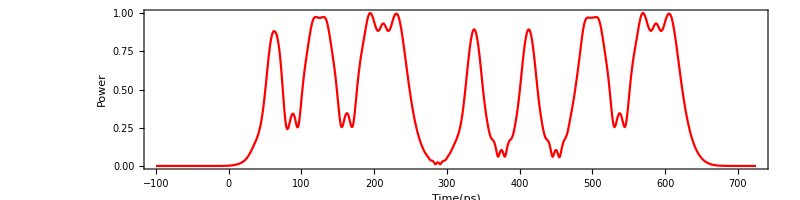

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

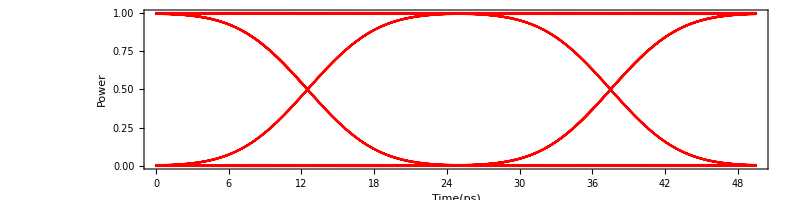

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

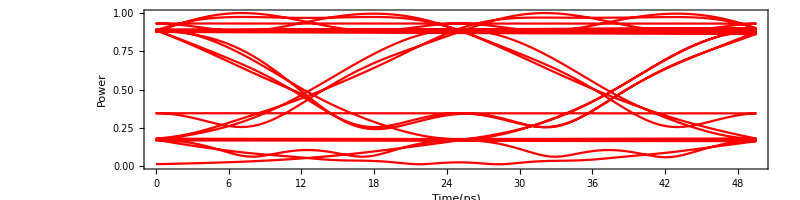

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 66 point

0 is 66 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.890548

Average of 0 is 0.200071

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.0392224

A Standard Deviation of 0 is 0.109323

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-167544.]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

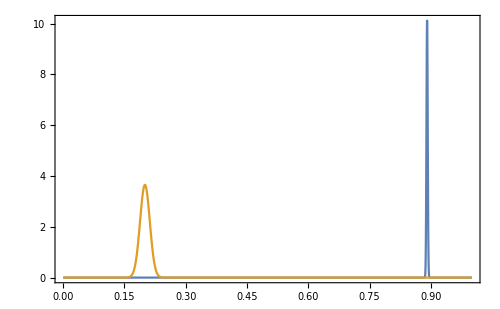

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 4.64825

Q-dB is 13.3458 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 1.67384×10^-6

Eye Opening is 0.784865

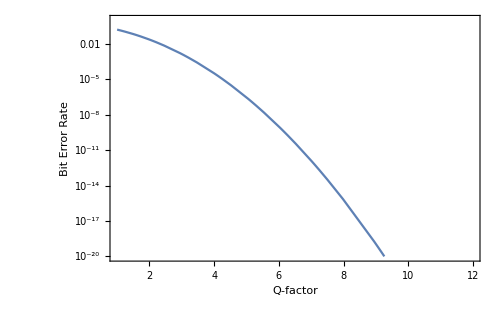

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```